```mathematica
findSum[f_,stepsize_,d_]:=If[d==1,Sum[f[i],{i,0,1,stepsize}],Sum[findSum[proj[f,i],stepsize,d-1],{i,0,1,stepsize}]]

totalSum[f_,stepsize_,d_]:=stepsize^d findSum[f,stepsize,d]
```

```mathematica
explicitSum[f_,stepsize_,d_]:=stepsize^d Sum[f@@x,##]&@@Sequence[Table[{x[i],0,1,stepsize},{i,1,d}]]
(*Use this one*)
```

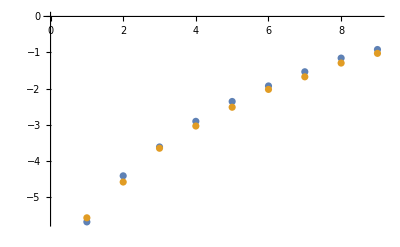

```mathematica
ListPlot[{Table[(1/n^2 Sum[i+j^2,{i,0,1,1/n},{j,0,1,1/n}]//Timing)[[1]],{n,100,500,50}],Table[(explicitSum[#[[1]]+#[[2]]^2&,1/n,2]//Timing)[[1]],{n,100,500,50}]}//Log2]
```

```mathematica
explicitSum[#1+#2^2&,1/300,2]
```

(90601 x)/90000